```mathematica
μ=0.62;
γ=5/3;
```

```mathematica
years=365.25*86400;
tEnd=10^3 years;
```

```mathematica
rper=0.7Rsun;
θper=45*Pi/180;
kRoss=21.1;
χ=(16*T[Rper,zper]^3*sigmaSB*(γ-1)*μ*mP)/(3*kRoss*ρ[Rper,zper]^2*kB);  (*this is what Goldreich and Schubert call χ*)
ξradiative = (γ-1)*χ ;    (*this is what Balbus and Schaan call ξrad*)

ν=23;   (*from Menou&Balbus2004*)

η=596;     (*from Menou&Balbus2004*)


Timing[Table[θper=θ;
ListofSolutions=Table[

M=Random[Integer,{-12.5,-3.5}];
kRexp=Random[Real,{M-1.5,M+1.5}];
kϕexp=Random[Real,{M-1.5,M+1.5}];
kzexp=Random[Real,{M-1.5,M+1.5}];
kR0=(-1)^Random[Integer,{0,1}](2Pi)/(10^kRexp Rsun);
kϕ0=(-1)^Random[Integer,{0,1}](2Pi)/(10^kϕexp Rsun);
kz0=(-1)^Random[Integer,{0,1}](2Pi)/(10^kzexp Rsun);
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvAexp=Random[Real,{-2,2}];
kdotvA=(-1)^Random[Integer,{0,1}]*10^kdotvAexp*Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vSqmod0=vR0^2+vz0^2;
SolveTheSystem;
vSqmod[t_]=δvRsol[t]^2+δvzsol[t]^2;
MaxVelocitySq=(Max[vSqmod[tEnd/10^6],vSqmod[tEnd/10^5],vSqmod[tEnd/10^4],vSqmod[tEnd/10^3],vSqmod[tEnd/10^2],vSqmod[tEnd/10^1],vSqmod[tEnd]])/vSqmod0;

{kR0,kϕ0,kz0,kdotvA,MaxVelocitySq} ,{q,1,10}];

ListofSolutions={θ,Sort[ListofSolutions, #1[[5]] > #2[[5]] &]};
PutAppend[ListofSolutions,"C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\RandomWavevectorTests\\Model C\\Model C - 2 - With Magnetic Field\\Model C with magnetic field - Results.txt"],{θ,5/180 Pi,85/180 Pi,10/180 Pi}]]
```

$Aborted

```mathematica
ListofSolutions
```

{(17 π)/36,{{-2.04442×10^-7,-1.2246×10^-7,-5.48238×10^-8,-0.0853773,0.985349},{0.0000925213,-2.8918×10^-6,0.0000153911,1.55534,0.96321},{1.46654×10^-6,-1.49424×10^-6,3.59034×10^-8,10.9442,0.904396},{-0.0000678897,0.00002671,-0.0000273756,0.414832,0.887324},{-7.81067×10^-6,-0.000172287,9.54839×10^-6,-1.20143,0.790232},{4.5982×10^-7,-2.83142×10^-6,0.00028309,-0.042478,0.773982},{1.73968×10^-7,-1.77672×10^-7,-9.41396×10^-8,0.0303603,0.77242},{5.72754×10^-6,0.0000112352,-0.000350249,-0.0535184,0.753594},{-6.74234×10^-6,-7.57214×10^-6,-2.03012×10^-7,-9.92315,0.700745},{-0.0000122945,1.59936×10^-7,3.45966×10^-8,0.686601,0.649419},{0.000585906,0.0000814851,3.93955×10^-6,-5.38119,0.567273},{2.85829×10^-8,8.75633×10^-6,4.78475×10^-8,-0.790827,0.341276},{-1.84466×10^-6,-0.0000456971,0.0000678999,0.119219,0.293527},{0.0000671643,0.000947097,-0.000285566,0.528225,0.238352},{3.57174×10^-8,-4.6109×10^-7,6.20565×10^-7,-0.114512,0.162438},{-3.70784×10^-8,2.74858×10^-7,-7.87148×10^-7,22.4965,0.143538},{1.19781×10^-6,4.87832×10^-6,-2.40448×10^-6,0.0253889,0.092776},{1.00749×10^-6,0.0000126816,0.0000614629,-5.11844,0.088779},{1.90878×10^-6,-0.000173745,-3.40046×10^-7,-93.1728,0.0756615},{8.27535×10^-6,-0.0000466113,-0.000014915,-19.6443,0.0427549},{9.72162×10^-6,0.00151358,-0.000134074,-0.0102854,0.0347778},{-0.0000958877,-0.00152787,0.0000103643,-1.51437,0.03347},{-0.000100467,-8.19517×10^-6,-0.0015996,0.0574076,0.0230493},{-3.19377×10^-7,5.74157×10^-7,0.000192424,-17.9211,0.0125035},{-2.19307×10^-6,-6.62991×10^-7,0.0000309615,-0.173523,0.000138951},{-0.00271105,0.000136492,0.000330401,13.0926,0.0000185632},{0.0000412733,-0.0028531,0.0000248168,-0.150668,7.26752×10^-6},{2.29085×10^-7,1.80652×10^-6,-0.0000167152,-3.21265,5.70679×10^-6},{-7.89009×10^-6,-1.45163×10^-6,0.0000175213,-0.0136144,3.21571×10^-7},{-0.00367609,0.000621619,-0.000134949,1.16914,1.49275×10^-9},{-0.000552206,0.00455416,0.00045833,0.0321164,3.11995×10^-14},{-0.000202127,-0.0049908,-0.000754062,27.3931,1.05202×10^-16},{0.0204539,-0.00534788,-0.00472402,1.14228,6.26921×10^-17},{0.00385534,-0.000568021,0.00509161,-25.9639,2.35514×10^-17},{0.0303656,0.000841965,0.00373243,0.0185556,1.22948×10^-17},{-0.0327807,-0.0328548,0.000712759,-10.4313,2.98377×10^-20},{0.000316464,0.00571079,-0.00163945,-0.149672,2.8771×10^-20},{0.00331837,-0.0266114,-0.00353908,-0.018638,1.79303×10^-20},{-0.00164869,-0.131681,-0.0485091,0.0189088,1.47523×10^-20},{0.0525972,-0.00658116,-0.0194857,91.8939,8.23384×10^-21},{-0.000611684,0.0212135,-0.00376816,-78.4534,5.53542×10^-22},{0.0263828,0.122233,0.00755853,-11.9334,1.13459×10^-22},{0.00152566,0.0107575,-0.0156435,8.13652,9.46817×10^-23},{-0.000412479,-0.00118439,-0.012157,3.67058,8.70338×10^-23},{-0.0346054,0.0572371,0.0446351,-92.0932,6.84683×10^-25},{-0.0947604,-0.00239181,0.0853929,0.0130476,1.75036×10^-25},{-0.318055,-0.0283315,0.325658,-28.193,5.13045×10^-28},{-0.287917,5.24066,-0.123318,-0.0109532,4.86163×10^-28},{0.000319762,-0.176104,-0.000322503,0.141725,3.47667×10^-30},{-0.00721787,0.0525134,0.00625899,0.0205557,6.00703×10^-32},{0.330382,0.137198,0.257032,0.0423196,3.29773×10^-32},{0.027171,-0.0343949,-0.0481404,29.5865,2.26686×10^-32},{-0.0149516,-0.0587612,0.00749894,-0.0949312,1.62559×10^-32},{-0.122134,-0.00117473,0.0160792,-1.33839,3.40706×10^-35},{1.56914,-0.158648,0.0817992,-55.9445,4.07008×10^-37},{-0.139331,-0.00762374,0.377769,-0.0223229,1.84448×10^-38},{0.0182001,-0.0494939,0.281683,-0.436032,8.34778×10^-40},{0.410939,2.33912,-3.54151,-0.0255334,1.18797×10^-40},{1.3592,0.0631493,0.0171098,-0.0843586,1.16562×10^-40},{0.328202,-0.100771,0.0119459,0.0824934,4.90715×10^-42},{0.0898415,-0.0648053,0.354977,-12.274,2.30289×10^-42},{-0.0101943,0.135445,-0.0476761,-2.72092,2.27255×10^-42},{0.00289547,-0.00763947,-0.235515,-0.155047,1.83742×10^-43},{-0.517572,0.00940476,-0.00374734,98.8413,2.67611×10^-47},{-0.527036,-0.849056,2.96965,0.847205,9.98279×10^-53},{2.89746,-0.589656,-5.18782,0.0143792,2.33533×10^-54},{5.17132,-9.83714,-1.0357,-2.34803,2.10927×10^-55},{1.25332,-0.794376,-2.84764,-35.1448,1.20504×10^-55},{22.871,-23.7008,0.0915387,26.7445,8.3657×10^-57},{-3.22209,-2.30501,-10.8062,76.5085,2.40337×10^-62},{-12.3073,2.30278,-0.235448,29.3525,3.92555×10^-64},{2.42335,-0.0678671,0.490191,73.0571,1.09202×10^-65},{0.0218612,-0.0339271,-0.853592,4.88114,8.85101×10^-66},{-4.78326,-18.1277,-0.958682,-0.484283,6.53457×10^-67},{22.3048,1.01469,0.518868,0.0277858,2.12943×10^-70},{-62.8804,-71.5322,8.97426,4.70023,8.87114×10^-73},{9.68491,24.9586,6.83868,0.121479,1.16124×10^-73},{95.8917,28.0049,-6.27695,-0.75022,8.09153×10^-77},{0.0306243,-15.456,-1.61227,-0.0203242,6.34512×10^-77},{41.8606,7.63479,2.0473,2.33607,1.35214×10^-77},{-1.75968,57.3716,0.38107,-0.612875,1.56428×10^-79},{1.06237,-33.28,3.84264,0.162242,6.29102×10^-81},{62.0965,-56.336,50.489,0.0110289,5.68823×10^-84},{-24.5723,-1.33748,19.8435,0.0717844,7.21094×10^-86},{-13.5177,133.236,-41.3279,-10.6348,2.39334×10^-88},{41.9438,99.254,9.96398,-4.40914,3.97376×10^-89},{30.3189,-10.9613,106.554,-0.0836591,9.389×10^-97},{0.196941,0.115597,10.6391,3.65389,2.35058×10^-97},{-4.47545,37.6881,47.5557,0.956262,5.18081×10^-99},{-417.073,483.134,6.43563,0.036715,1.21463×10^-100},{-39.1007,183.331,176.433,2.1694,7.66276×10^-101},{-490.84,-134.237,-220.626,-2.52043,2.36444×10^-102},{-202.715,6.67101,126.918,0.0779475,8.96834×10^-109},{469.386,67.6485,-12.6319,1.43917,5.95425×10^-111},{215.397,1.6426,-4.6973,3.39459,2.30896×10^-116},{-158.033,-731.486,622.924,-0.117387,1.1119×10^-123},{-517.929,-1811.21,-4.2816,4.04686,1.58737×10^-124},{175.434,0.860015,24.8097,-28.5235,3.12146×10^-128},{157.267,-255.787,-760.068,0.0156476,3.36792×10^-134},{-19.5649,-5.17414,-2122.52,0.215396,1.25716×10^-196}}}

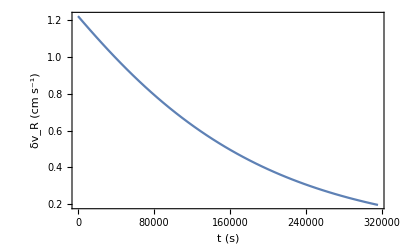

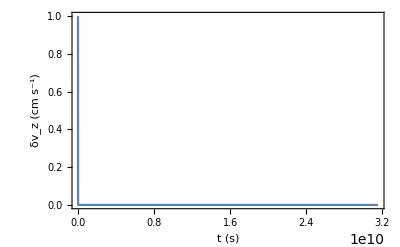

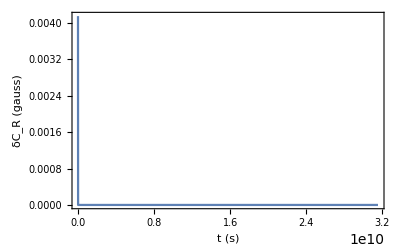

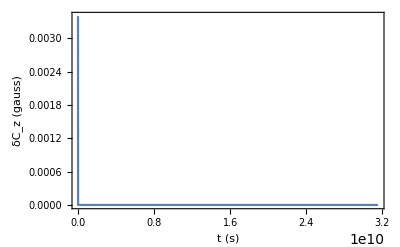

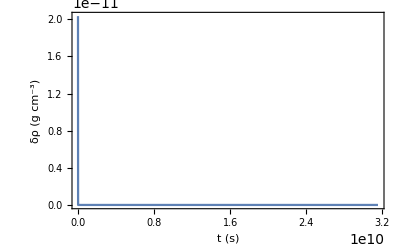

```mathematica
Plot[δvRsol[t],{t,0,tEnd/100000},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δv_R (cm s^-1)","Test 08 - δv_R(t)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δvzsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δv_z (cm s^-1)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δCRsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δC_R (gauss)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δCzsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δC_z (gauss)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
Plot[δρsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δρ (g cm^-3)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
```

```mathematica
kRexp=Random[Real,{M-1.5,M+1.5}];
kϕexp=Random[Real,{M-1.5,M+1.5}];
kzexp=Random[Real,{M-1.5,M+1.5}];
kR0=2.1*10^-4;
kϕ0=4.2*10^-7;
kz0=1.3*10^-5;
kR[t_]=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]=kϕ0;
kz[t_]=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kdotvA=100Ω[Rper,zper];

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;

vmod0=√(vR0^2+vz0^2);
TimeConstrained[SolveTheSystem,5];
```

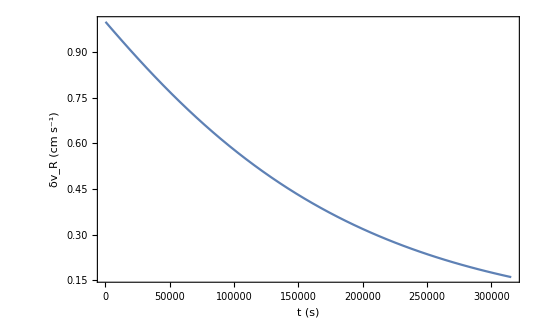

```mathematica
Plot[δvRsol[t]/δvRsol[0],{t,0,tEnd/100000},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δv_R (cm s^-1)","Test 08 - δv_R(t)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
```